```mathematica
nf1x[ξ_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1}];

nf2x[ξ_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1}];

nf3x[ξ_]=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,P1->1,Λ->1,t->-1}];
```

```mathematica
(*积分范围记得要改变*)
```

```mathematica
(*yFms[ξ_]:=NIntegrate[y*nf1x[ξ],{y,-ξ,ξ},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[y*nf2x[ξ],{y,ξ,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

```mathematica
yFoct[ξ_]:=NIntegrate[(1-y)*nf1x[ξ],{y,0,1-ξ},{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[(1-y)*nf2x[ξ],{y,1-ξ,1+ξ},{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[nf3x[ξ],{k3,0,∞},{θ,0,2π},{x,0,1},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
(*NIntegrate[(1-y)*nf2x[ξ],{y,1-ξ,1+ξ},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

```mathematica
(*lyf=ParallelTable[{ξ,yFms[ξ]},{ξ,0.01,0.4,0.01}];
syf=Interpolation[lyf];
```

```mathematica
yFoct[0.01]
```

-1.203275244+4.329536067×10^-21 ⅈ

```mathematica
yFoct[0.001]
```

-1.203147581+4.327167294×10^-23 ⅈ

```mathematica
yFoct[0.0001]
```

-1.203146302+4.327147514×10^-25 ⅈ

```mathematica
lyf=ParallelTable[{ξ,I*yFoct[ξ]},{ξ,0.01,0.4,0.01}];
syf=Interpolation[lyf];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.399984} lies outside the range of data in the interpolating function. Extrapolation will be used.

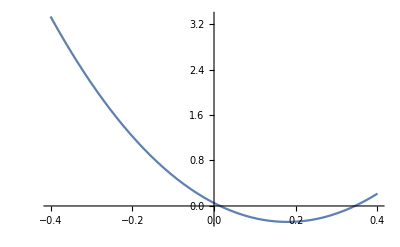

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Plot[syf[x],{x,-0.4,0.4}]
```

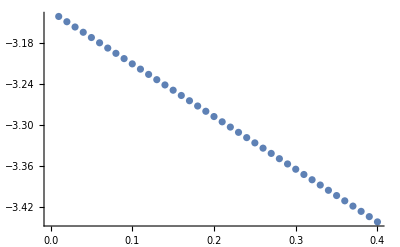

```mathematica
ListPlot[lyf]
```

```mathematica
lyf
```

{{0.01,-0.00584924+0. ⅈ},{0.02,0.0405254+0. ⅈ},{0.03,0.086872+0. ⅈ},{0.04,0.133192+0. ⅈ},{0.05,0.179485+0. ⅈ},{0.06,0.225774+0. ⅈ},{0.07,0.272013+0. ⅈ},{0.08,0.318231+0. ⅈ},{0.09,0.364459+0. ⅈ},{0.1,0.410616+0. ⅈ},{0.11,0.456744+0. ⅈ},{0.12,0.502848+0. ⅈ},{0.13,0.548925+0. ⅈ},{0.14,0.594973+0. ⅈ},{0.15,0.640994+0. ⅈ},{0.16,0.686988+0. ⅈ},{0.17,0.732956+0. ⅈ},{0.18,0.778895+0. ⅈ},{0.19,0.824808+0. ⅈ},{0.2,0.870693+0. ⅈ},{0.21,0.916552+0. ⅈ},{0.22,0.962383+0. ⅈ},{0.23,1.00819+0. ⅈ},{0.24,1.05396+0. ⅈ},{0.25,1.09971+0. ⅈ},{0.26,1.14544+0. ⅈ},{0.27,1.19113+0. ⅈ},{0.28,1.2368+0. ⅈ},{0.29,1.28242+0. ⅈ},{0.3,1.32801+0. ⅈ},{0.31,1.37364+0. ⅈ},{0.32,1.41916+0. ⅈ},{0.33,1.46469+0. ⅈ},{0.34,1.51024+0. ⅈ},{0.35,1.55567+0. ⅈ},{0.36,1.60113+0. ⅈ},{0.37,1.6466+0. ⅈ},{0.38,1.69199+0. ⅈ},{0.39,1.73736+0. ⅈ},{0.4,1.78271+0. ⅈ}}

```mathematica
lyf
```

{{0.01,0.0986796+0. ⅈ},{0.02,0.145135+0. ⅈ},{0.03,0.191619+0. ⅈ},{0.04,0.238129+0. ⅈ},{0.05,0.284666+0. ⅈ},{0.06,0.33123+0. ⅈ},{0.07,0.377799+0. ⅈ},{0.08,0.424418+0. ⅈ},{0.09,0.47106+0. ⅈ},{0.1,0.517685+0. ⅈ},{0.11,0.564385+0. ⅈ},{0.12,0.611113+0. ⅈ},{0.13,0.657868+0. ⅈ},{0.14,0.704649+0. ⅈ},{0.15,0.751457+0. ⅈ},{0.16,0.798294+0. ⅈ},{0.17,0.845156+0. ⅈ},{0.18,0.892046+0. ⅈ},{0.19,0.938963+0. ⅈ},{0.2,0.985907+0. ⅈ},{0.21,1.03288+0. ⅈ},{0.22,1.07988+0. ⅈ},{0.23,1.1269+0. ⅈ},{0.24,1.17396+0. ⅈ},{0.25,1.22104+0. ⅈ},{0.26,1.26814+0. ⅈ},{0.27,1.31528+0. ⅈ},{0.28,1.36244+0. ⅈ},{0.29,1.40963+0. ⅈ},{0.3,1.45685+0. ⅈ},{0.31,1.50409+0. ⅈ},{0.32,1.55136+0. ⅈ},{0.33,1.59866+0. ⅈ},{0.34,1.64598+0. ⅈ},{0.35,1.69333+0. ⅈ},{0.36,1.74071+0. ⅈ},{0.37,1.78812+0. ⅈ},{0.38,1.83555+0. ⅈ},{0.39,1.88301+0. ⅈ},{0.4,1.9305+0. ⅈ}}

```mathematica
lyf1={{0.01,0.09867960619486293+0. ⅈ},{0.02,0.1451351454833203+0. ⅈ},{0.03,0.19161903596825036+0. ⅈ},{0.04,0.23812877403520094+0. ⅈ},{0.05,0.28466644128370744+0. ⅈ},{0.06,0.33123045970838794+0. ⅈ},{0.06999999999999999,0.3777986024207176+0. ⅈ},{0.07999999999999999,0.42441774576375124+0. ⅈ},{0.09,0.4710597333841644+0. ⅈ},{0.09999999999999999,0.5176847283692068+0. ⅈ},{0.10999999999999999,0.5643848792550505+0. ⅈ},{0.12,0.6111126798322122+0. ⅈ},{0.13,0.6578676223676172+0. ⅈ},{0.14,0.7046491550855725+0. ⅈ},{0.15,0.7514569691274531+0. ⅈ},{0.16,0.7982935898803774+0. ⅈ},{0.17,0.8451560503007551+0. ⅈ},{0.18,0.8920461668856101+0. ⅈ},{0.19,0.9389629211229373+0. ⅈ},{0.2,0.9859073497476178+0. ⅈ},{0.21,1.0328788892020926+0. ⅈ},{0.22,1.0798777395001358+0. ⅈ},{0.23,1.1269036935193266+0. ⅈ},{0.24,1.1739567377666822+0. ⅈ},{0.25,1.2210373912256691+0. ⅈ},{0.26,1.2681449924787296+0. ⅈ},{0.27,1.3152796925047903+0. ⅈ},{0.28,1.362441552938696+0. ⅈ},{0.29000000000000004,1.409630249441537+0. ⅈ},{0.30000000000000004,1.45684608298694+0. ⅈ},{0.31,1.5040886171269652+0. ⅈ},{0.32,1.5513580691260709+0. ⅈ},{0.33,1.5986552966319982+0. ⅈ},{0.34,1.6459791163543418+0. ⅈ},{0.35000000000000003,1.6933300827996631+0. ⅈ},{0.36000000000000004,1.7407104611626494+0. ⅈ},{0.37,1.7881165516628448+0. ⅈ},{0.38,1.835549020557671+0. ⅈ},{0.39,1.883008834105361+0. ⅈ},{0.4,1.9304964314952182+0. ⅈ}};
```

```mathematica
syf1=Interpolation[lyf1];
```

InterpolatingFunction::dmval: Input value {-0.449983} lies outside the range of data in the interpolating function. Extrapolation will be used.

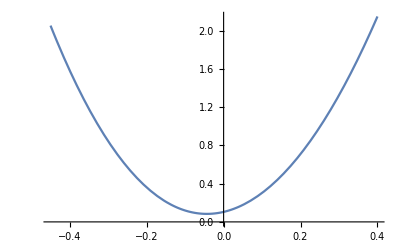

```mathematica
Plot[syf1[x]+syf[x],{x,-0.45,0.4}]
```

```mathematica
test[x_]=syf1[x]+syf[x];
```

```mathematica
test[0.1]
```

0.9283

```mathematica
test[0.2]
```

1.8566

```mathematica
test[0.3]
```

2.78486

```mathematica
test[0.4]
```

3.71321